```mathematica
Clear["GLobals`*"]
```

----- Creamos una función ------
 Module [ { Inicializamos los valores separados por comas } , Función [ ] : = Escribimos la función ]

```mathematica
Module[{a=314159269,c=453806245,m=2^31,z=1000},RndData[]:= (z=Mod[z*a+c,m])/m //N
]
```

```mathematica
RndData[]
```

0.50313

----- Recogemos muestras -----

```mathematica
muestras =Table[RndData[],100000];
```

```mathematica
muestras[[1;;20]]
```

{0.607222,0.243107,0.292092,0.411891,0.145711,0.126371,0.513474,0.0849767,0.498178,0.408791,0.383209,0.169938,0.832972,0.0415893,0.534402,0.599613,0.734372,0.323467,0.528235,0.408409}

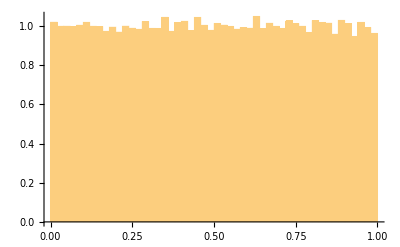

```mathematica
Histogram[muestras,30,PDF]
```

----- Creamos la función exponencial -----

```mathematica
RndExp[rate_]:=-Log[RndData[]]/rate;
```

```mathematica
muestras2=Table[RndExp[100],10000];
muestras2[[1;;20]]
```

{0.0164907,0.00441075,0.0106288,0.0115854,0.00421196,0.000134437,0.00873431,0.0180808,0.00288001,0.00490092,0.0299081,0.0182226,0.00292222,0.00454523,0.00855301,0.00742335,0.000565737,0.00105308,0.0120636,0.0156734}

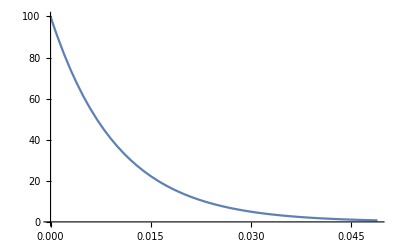

```mathematica
g1=Plot[100*E^(-100*t),{t,0,0.049}]
```

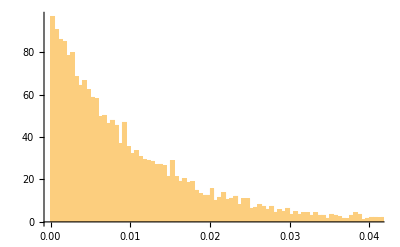

```mathematica
h1=Histogram[muestras2,200,PDF]
```

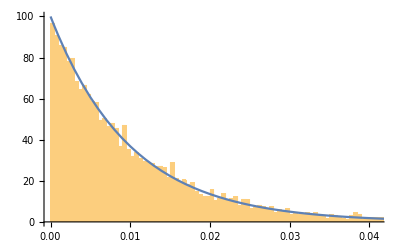

```mathematica
Show [h1,g1]
```

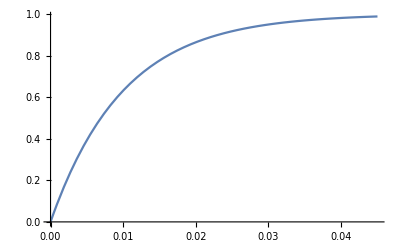

```mathematica
g=Plot[1-E^(-100*t),{t,0,0.045}]
```

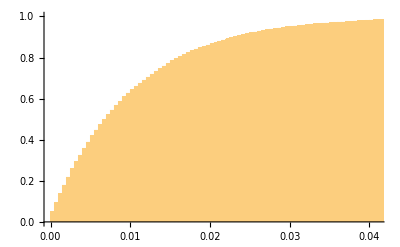

```mathematica
h=Histogram[muestras2,125,CDF]
```

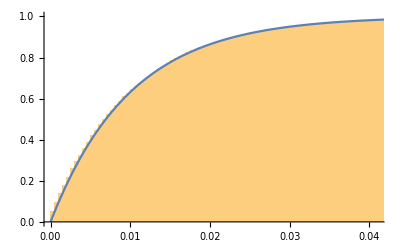

```mathematica
Show[h,g]
```